```mathematica
SetDirectory @ NotebookDirectory[];
Import["QuEST.m"];
Install["quest_link_GPU"];
```

Childs’ motivated Ising Hamiltonian, to be studied to time t=n for self-thermalization
	https://arxiv.org/pdf/1711.10980.pdf

```mathematica
getHamil[n_] :=
	Table[Subscript[σ, q-1] Subscript[σ, Mod[q,n]],{σ,{X,Y,Z}},{q,n}] ~Join~ Table[RandomReal[{-1,1}] Subscript[Z, q-1],{q,n}] // Flatten
```

```mathematica
Exp[ⅈ Plus @@ getHamil[5]]
```

ⅇ^(ⅈ (X_0 X_1+X_1 X_2+X_2 X_3+X_0 X_4+X_3 X_4+Y_0 Y_1+Y_1 Y_2+Y_2 Y_3+Y_0 Y_4+Y_3 Y_4-0.124857 Z_0-0.179461 Z_1+Z_0 Z_1+0.577474 Z_2+Z_1 Z_2-0.763526 Z_3+Z_2 Z_3-0.740377 Z_4+Z_0 Z_4+Z_3 Z_4))

Suzuki symmetrization:
	https://arxiv.org/pdf/math-ph/0506007.pdf

```mathematica
symmetrize[hamil_List, λ_, 1] := (λ hamil)
symmetrize[hamil_List, λ_, 2] := With[{s1 = symmetrize[hamil, λ/2, 1]}, Join[s1,Reverse[s1]]]
symmetrize[hamil_List, λ_, n_?EvenQ] := 
	Block[{γ, p=1/(4-4^(1/(n-1)))}, 
		With[{s=symmetrize[hamil,γ,n-2]}, {r=s /. γ -> λ p},
			Join[r, r, s /. γ -> (1-4p)λ, r, r]]]
			
trotterize[hamil_List, order_, reps_, time_] :=
	With[{s=symmetrize[hamil, N @ time/reps, order]},
		Flatten @ ConstantArray[s, reps]]
```

```mathematica
getGate[Verbatim[Times][θ:_?NumericQ:1, σ:__]] := R[2 θ, Times[σ]]
getCircuit[terms_List] := getGate /@ terms
```

```mathematica
getCircuit @ trotterize[getHamil[4],2,1,4]
```

{R[4.,X_0 X_1],R[4.,X_1 X_2],R[4.,X_2 X_3],R[4.,X_0 X_3],R[4.,Y_0 Y_1],R[4.,Y_1 Y_2],R[4.,Y_2 Y_3],R[4.,Y_0 Y_3],R[4.,Z_0 Z_1],R[4.,Z_1 Z_2],R[4.,Z_2 Z_3],R[4.,Z_0 Z_3],R[-2.08598,Z_0],R[0.6062,Z_1],R[2.91228,Z_2],R[0.0162906,Z_3],R[0.0162906,Z_3],R[2.91228,Z_2],R[0.6062,Z_1],R[-2.08598,Z_0],R[4.,Z_0 Z_3],R[4.,Z_2 Z_3],R[4.,Z_1 Z_2],R[4.,Z_0 Z_1],R[4.,Y_0 Y_3],R[4.,Y_2 Y_3],R[4.,Y_1 Y_2],R[4.,Y_0 Y_1],R[4.,X_0 X_3],R[4.,X_2 X_3],R[4.,X_1 X_2],R[4.,X_0 X_1]}

```mathematica
getCircuit @ trotterize[getHamil[6],2,1,6]
```

{R[6.,X_0 X_1],R[6.,X_1 X_2],R[6.,X_2 X_3],R[6.,X_3 X_4],R[6.,X_4 X_5],R[6.,X_0 X_5],R[6.,Y_0 Y_1],R[6.,Y_1 Y_2],R[6.,Y_2 Y_3],R[6.,Y_3 Y_4],R[6.,Y_4 Y_5],R[6.,Y_0 Y_5],R[6.,Z_0 Z_1],R[6.,Z_1 Z_2],R[6.,Z_2 Z_3],R[6.,Z_3 Z_4],R[6.,Z_4 Z_5],R[6.,Z_0 Z_5],R[0.645653,Z_0],R[5.96344,Z_1],R[-3.26118,Z_2],R[3.98073,Z_3],R[0.349657,Z_4],R[-1.54349,Z_5],R[-1.54349,Z_5],R[0.349657,Z_4],R[3.98073,Z_3],R[-3.26118,Z_2],R[5.96344,Z_1],R[0.645653,Z_0],R[6.,Z_0 Z_5],R[6.,Z_4 Z_5],R[6.,Z_3 Z_4],R[6.,Z_2 Z_3],R[6.,Z_1 Z_2],R[6.,Z_0 Z_1],R[6.,Y_0 Y_5],R[6.,Y_4 Y_5],R[6.,Y_3 Y_4],R[6.,Y_2 Y_3],R[6.,Y_1 Y_2],R[6.,Y_0 Y_1],R[6.,X_0 X_5],R[6.,X_4 X_5],R[6.,X_3 X_4],R[6.,X_2 X_3],R[6.,X_1 X_2],R[6.,X_0 X_1]}

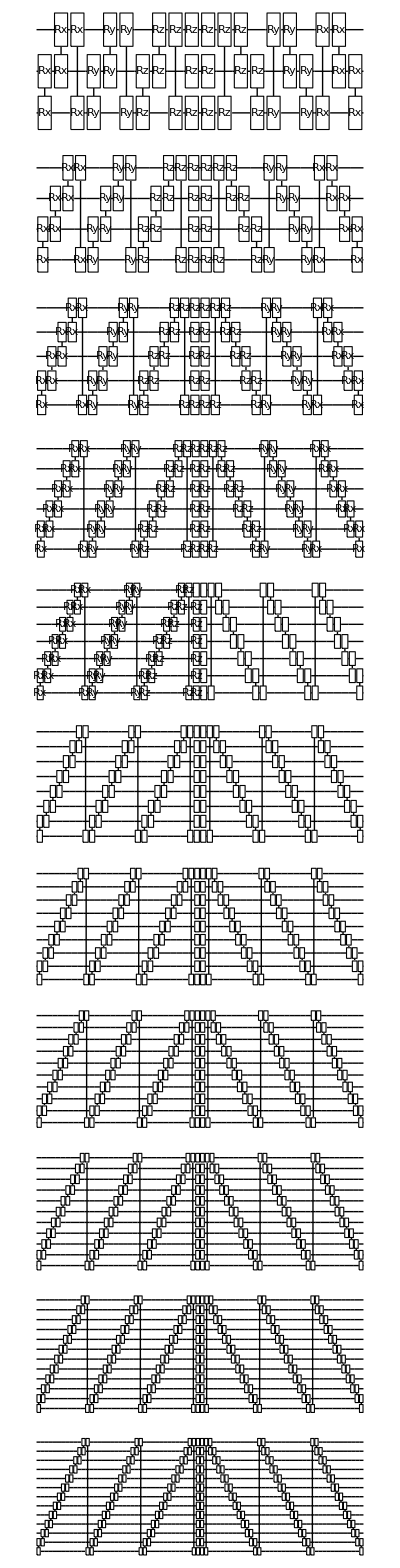

```mathematica
Column @ Table[
	DrawCircuit @ getCircuit @ trotterize[getHamil[n],2,1,n],
	{n,3,13}
]
```

## Motivating input circuit

```mathematica
getHamilTermMatrix[numQb_][Verbatim[Times][θ:_?NumericQ:1, σ:__]] := 
	θ KroneckerProduct @@ Fold[
		ReplacePart[#1, (numQb-#2⟦2⟧) -> PauliMatrix[#2⟦1⟧/.{X->1,Y->2,Z->3}]]&,
		Table[IdentityMatrix[2],numQb], {σ}]
		
getHamilMatrix[hamil_List] :=
	getHamilTermMatrix[1+Max@Cases[hamil,Subscript[_, q_]:>q,∞]] /@ hamil // Total
	
getTrueEvol[hamil_List, initψ_, duration_] :=
	MatrixExp[-ⅈ duration getHamilMatrix[hamil]] . initψ
```

```mathematica
DestroyAllQuregs[];
```

```mathematica
n=5;
h = getHamil[n];
u = getCircuit @ trotterize[h,2,1,n];
ψ = CreateQureg[n];
ApplyCircuit[u, ψ];

ϕ = CreateQureg[n];
SetQuregMatrix[ϕ, getTrueEvol[h,GetQuregMatrix[ϕ],n]];

CalcFidelity[ψ,ϕ]
Length[u]
```

0.00323827

40

```mathematica
DestroyAllQuregs[];
```

## Motivating output circuit

```mathematica
Subscript[pSwap, a_,b_] := Subscript[U, a,b][({{1, 0, 0, 0}, {0, 0, Exp[ⅈ #], 0}, {0, Exp[ⅈ #], 0, 0}, {0, 0, 0, 1}})]&
getRecompCircuit[n_] := Module[{gates},
gates = Flatten@ConstantArray[{Transpose @ Table[{Subscript[Rz, q],Subscript[Rx, q],Subscript[Ry, q],Subscript[Rz, q]},{q,0,n-1}], Table[Subscript[pSwap, q,Mod[q+1,n]], {q,0,n-1}]}, 2];
gates = Join[gates, Reverse[gates]];
AppendTo[gates, G];
MapThread[Compose, {gates, Table[Subscript[θ, t],{t,Length[gates]}]}]]
```

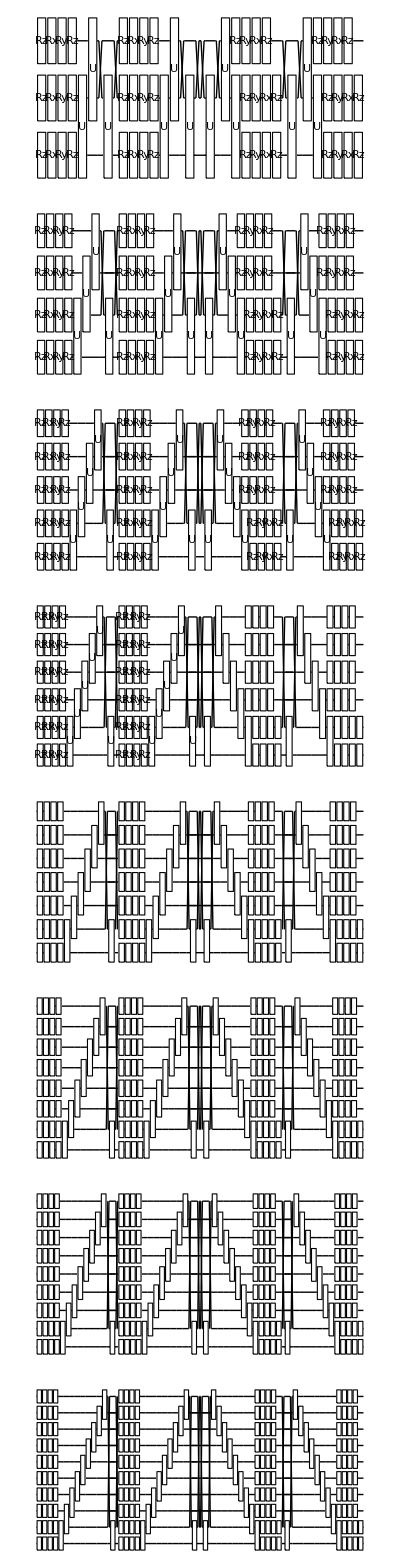

```mathematica
Column @ Table[
	DrawCircuit[getRecompCircuit[n], n],
	{n,3,10}
]
```

32

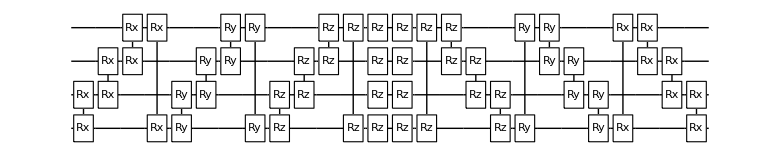

```mathematica
getCircuit @ trotterize[getHamil[4],2,1,1];
Length@%
DrawCircuit[%%]
```

{Rz_0[θ_1],Rz_1[θ_2],Rz_2[θ_3],Rz_3[θ_4],Rx_0[θ_5],Rx_1[θ_6],Rx_2[θ_7],Rx_3[θ_8],Ry_0[θ_9],Ry_1[θ_10],Ry_2[θ_11],Ry_3[θ_12],Rz_0[θ_13],Rz_1[θ_14],Rz_2[θ_15],Rz_3[θ_16],U_(0,1)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_17),0},{0,ⅇ^(ⅈ θ_17),0,0},{0,0,0,1}}],U_(1,2)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_18),0},{0,ⅇ^(ⅈ θ_18),0,0},{0,0,0,1}}],U_(2,3)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_19),0},{0,ⅇ^(ⅈ θ_19),0,0},{0,0,0,1}}],U_(3,0)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_20),0},{0,ⅇ^(ⅈ θ_20),0,0},{0,0,0,1}}],Rz_0[θ_21],Rz_1[θ_22],Rz_2[θ_23],Rz_3[θ_24],Rx_0[θ_25],Rx_1[θ_26],Rx_2[θ_27],Rx_3[θ_28],Ry_0[θ_29],Ry_1[θ_30],Ry_2[θ_31],Ry_3[θ_32],Rz_0[θ_33],Rz_1[θ_34],Rz_2[θ_35],Rz_3[θ_36],U_(0,1)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_37),0},{0,ⅇ^(ⅈ θ_37),0,0},{0,0,0,1}}],U_(1,2)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_38),0},{0,ⅇ^(ⅈ θ_38),0,0},{0,0,0,1}}],U_(2,3)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_39),0},{0,ⅇ^(ⅈ θ_39),0,0},{0,0,0,1}}],U_(3,0)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_40),0},{0,ⅇ^(ⅈ θ_40),0,0},{0,0,0,1}}],U_(3,0)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_41),0},{0,ⅇ^(ⅈ θ_41),0,0},{0,0,0,1}}],U_(2,3)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_42),0},{0,ⅇ^(ⅈ θ_42),0,0},{0,0,0,1}}],U_(1,2)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_43),0},{0,ⅇ^(ⅈ θ_43),0,0},{0,0,0,1}}],U_(0,1)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_44),0},{0,ⅇ^(ⅈ θ_44),0,0},{0,0,0,1}}],Rz_3[θ_45],Rz_2[θ_46],Rz_1[θ_47],Rz_0[θ_48],Ry_3[θ_49],Ry_2[θ_50],Ry_1[θ_51],Ry_0[θ_52],Rx_3[θ_53],Rx_2[θ_54],Rx_1[θ_55],Rx_0[θ_56],Rz_3[θ_57],Rz_2[θ_58],Rz_1[θ_59],Rz_0[θ_60],U_(3,0)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_61),0},{0,ⅇ^(ⅈ θ_61),0,0},{0,0,0,1}}],U_(2,3)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_62),0},{0,ⅇ^(ⅈ θ_62),0,0},{0,0,0,1}}],U_(1,2)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_63),0},{0,ⅇ^(ⅈ θ_63),0,0},{0,0,0,1}}],U_(0,1)[{{1,0,0,0},{0,0,ⅇ^(ⅈ θ_64),0},{0,ⅇ^(ⅈ θ_64),0,0},{0,0,0,1}}],Rz_3[θ_65],Rz_2[θ_66],Rz_1[θ_67],Rz_0[θ_68],Ry_3[θ_69],Ry_2[θ_70],Ry_1[θ_71],Ry_0[θ_72],Rx_3[θ_73],Rx_2[θ_74],Rx_1[θ_75],Rx_0[θ_76],Rz_3[θ_77],Rz_2[θ_78],Rz_1[θ_79],Rz_0[θ_80],G[θ_81]}

81

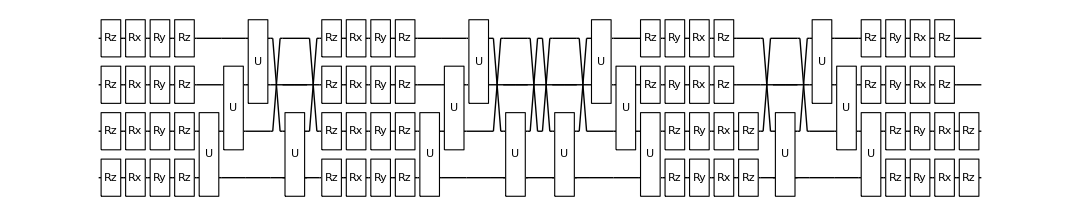

```mathematica
getRecompCircuit[4]
Length[%]
DrawCircuit[%%,4]
```

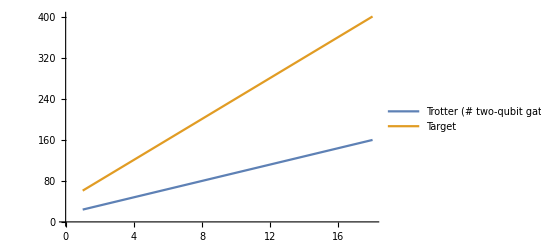

```mathematica
ListLinePlot[
	{Table[Length @ getCircuit @ trotterize[getHamil[qb],2,1,1], {qb,3,20}],
	Table[Length @getRecompCircuit[qb], {qb,3,20}]},Ticks->{None,Automatic},
	PlotLegends-> {"Trotter (# two-qubit gates)", "Target"}
]
```

## Energy calcs

Optimised energy calculations under Hamiltonian 1 - |0><0|

```mathematica
calcEnergy[ψ_] :=
	1 - Abs[GetAmp[ψ, 0]]^2

calcEnergyGrad[ψ_, dψ_] :=
	Table[Re[CalcInnerProduct[ψ,dψdp] - Conjugate[GetAmp[ψ,0]] GetAmp[dψdp,0]],{dψdp, dψ}]
```

### testing Mathematica’s inbuilt optimisation

```mathematica
DestroyAllQuregs[];

numQb =5;
hamil = getHamil[numQb];
aCirc = getCircuit @ trotterize[hamil,2,1,numQb];
bCirc = getRecompCircuit[numQb] /. Subscript[θ, n_]:> Symbol["θ"<>ToString[n]];
numParams =Length[bCirc];

{Aψ,Bψ} = CreateQuregs[numQb, 2];
ApplyCircuit[aCirc, InitZeroState[Aψ]];
```

```mathematica
Clear[calcEnergyFromParams]

calcEnergyFromParams[vals__?NumericQ] :=
	Block[{params = MapIndexed[Symbol["θ"<>ToString[#2⟦1⟧]]->#1&, {vals}]},
		ApplyCircuit[bCirc /. params, InitPureState[Bψ,Aψ]];
		calcEnergy[Bψ]]
```

```mathematica
calcEnergyFromParams @@ Table[RandomReal[], numParams]
```

0.99648

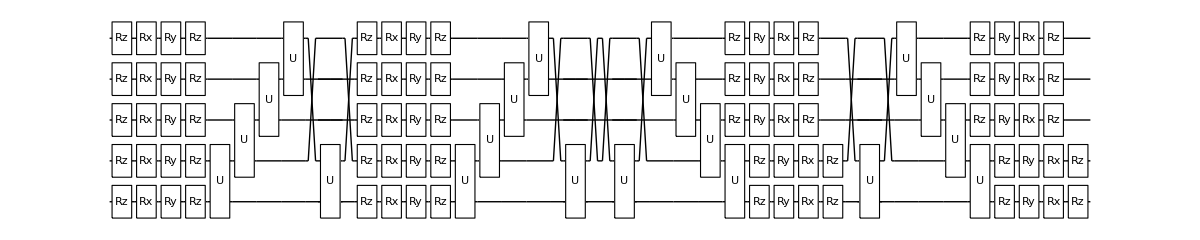

```mathematica
DrawCircuit[bCirc, numQb]
```

```mathematica
symbs = Table[Symbol["θ" <> ToString[n]], {n,numParams}];
cons = Map[0 < # < 4π&, symbs];

NMinimize[
	{calcEnergyFromParams @@ symbs, Sequence @@ cons},
	
	symbs,
	(*Transpose[{symbs, RandomReal[{-π,π},numParams]}],*)
	
	Method -> "NelderMead",
	AccuracyGoal->6
]
```

{0.016094,{θ1→2.58329,θ2→8.77848,θ3→5.00583,θ4→2.66142,θ5→3.52088,θ6→2.34469,θ7→7.85394,θ8→7.85446,θ9→4.71239,θ10→5.24416,θ11→4.71239,θ12→1.96402,θ13→4.65432,θ14→6.38577,θ15→4.7124,θ16→2.61476,θ17→3.42801,θ18→2.46365,θ19→1.87594,θ20→4.52742,θ21→2.45278,θ22→4.60495,θ23→3.71222,θ24→7.19632,θ25→4.86059,θ26→6.06275,θ27→3.58274,θ28→5.96159,θ29→2.5149,θ30→2.81373,θ31→7.08505,θ32→3.07793,θ33→1.57075,θ34→7.85396,θ35→4.71237,θ36→4.74942,θ37→3.39999,θ38→4.69595,θ39→7.57409,θ40→3.183,θ41→3.85548,θ42→3.29615,θ43→6.88052,θ44→2.91183,θ45→2.38766,θ46→3.30117,θ47→2.7643,θ48→2.73923,θ49→9.61941,θ50→7.82018,θ51→7.53592,θ52→4.51776,θ53→1.97316,θ54→8.23128,θ55→3.61078,θ56→3.88918,θ57→8.81451,θ58→5.26062,θ59→7.45637,θ60→3.1963,θ61→2.99223,θ62→6.81856,θ63→6.10752,θ64→6.34367,θ65→10.5531,θ66→3.64437,θ67→2.84178,θ68→8.45815,θ69→6.16975,θ70→7.85399,θ71→3.16227,θ72→7.66167,θ73→4.12103,θ74→6.88473,θ75→8.63723,θ76→2.24639,θ77→4.97554,θ78→3.85605,θ79→4.7124,θ80→2.13956,θ81→6.53576,θ82→4.94012,θ83→3.03115,θ84→10.2445,θ85→9.59635,θ86→3.81235,θ87→2.83155,θ88→2.58336,θ89→3.14377,θ90→4.86631,θ91→8.88708,θ92→2.24941,θ93→7.85396,θ94→8.36151,θ95→2.95321,θ96→8.44494,θ97→4.26029,θ98→4.62242,θ99→3.05584,θ100→9.21241,θ101→8.59581}}

```mathematica
mytest[x_,y_] := x^2+1 - y^2
```

```mathematica
NMinimize[{mytest[x,y], -2 < x<-1, 1 > y>0}, {x,y}]
```

{1.,{x→-1.,y→1.}}

```mathematica
1 - 0.01609399093316566
```

0.983906

## Time-adapative recompilation

Dynamic time-step adaptation

```mathematica
paramMapper = MapIndexed[Subscript[θ, #2⟦1⟧]->#1&];

sampleTimestep[Δt_, θ_, Δθ_, prevE_, aψ_, bψ_, bCirc_] := (
	ApplyCircuit[bCirc /. paramMapper[θ + Δt Δθ], InitPureState[bψ, aψ]];
	calcEnergy[bψ] - prevE)

sampleTimesteps[Δt_, θ_, Δθ_, prevE_, aψ_, bψ_, bCirc_, {None,None,None}] :=
	Table[
		sampleTimestep[Δtchoice, θ, Δθ, prevE, aψ, bψ, bCirc],
		{Δtchoice, {Δt/2., Δt, 2.Δt}}];
	
sampleTimesteps[Δt_, θ_, Δθ_, prevE_, aψ_, bψ_, bCirc_, samples_List] :=
	If[
		samples⟦1⟧ === None,
		{sampleTimestep[Δt/2.,θ, Δθ, prevE, aψ, bψ, bCirc], samples⟦2⟧, samples⟦3⟧},
		{samples⟦1⟧, samples⟦2⟧, sampleTimestep[2.Δt, θ, Δθ, prevE, aψ, bψ, bCirc]}]

chooseTimestep[Δt_, θ_, Δθ_, prevE_, aψ_, bψ_, bCirc_, samples_:{None,None,None}] :=
	Module[{tA,tB,tC, tBest},
		{tA,tB,tC} = sampleTimesteps[Δt, θ, Δθ, prevE, aψ, bψ, bCirc, samples];
		tBest = Min[tA,tB,tC];
		Which[
			Abs[tBest] < 10^-8,
			Δt,
			tBest > 0,
			chooseTimestep[Δt/8., θ, Δθ, prevE, aψ, bψ, bCirc],
			tBest === tC,
			chooseTimestep[2.Δt, θ, Δθ, prevE, aψ, bψ, bCirc, {tB,tC,None}],
			tBest === tA,
			chooseTimestep[Δt/2., θ, Δθ, prevE, aψ, bψ, bCirc, {None,tA,tB}],
			tBest === tB,
			Δt]]
```

Variational imaginary time evolution

```mathematica
simImag[aψ_, bCirc_, bψ_, dψ_, initparams_, steps_, timestep_:Null] := Module[
	{params, matrA, vecC, energy, Δt, Δθ, energyLog={},paramLog={},ΔtLog={}},
		
		Δt = If[timestep === Null, 1, timestep];
		params = initparams;
		
		ApplyCircuit[bCirc /. params, InitPureState[bψ, aψ]];
		energy = calcEnergy[bψ];
		
		Do[
			CalcQuregDerivs[bCirc, aψ, params, dψ];
			matrA = Re @ CalcInnerProducts[dψ];

			ApplyCircuit[bCirc /. params, InitPureState[bψ, aψ]];
			vecC = - Re @ calcEnergyGrad[bψ, dψ];

			(* Δθ = LinearSolve[matrA, vecC]; *)
			Δθ = PseudoInverse[matrA] . vecC;
			Δt = If[
				timestep === Null,
				chooseTimestep[Δt, params⟦All,2⟧, Δθ, energy, aψ, bψ, bCirc],
				timestep];
			params = paramMapper[params⟦All,2⟧ + Δt Δθ];
		
			ApplyCircuit[bCirc /. params, InitPureState[bψ, aψ]];
			energy = calcEnergy[bψ];
			
			AppendTo[energyLog, energy];
			AppendTo[paramLog, params⟦All,2⟧];
			AppendTo[ΔtLog, Δt];
		
			Null, steps];
			
		{energyLog, paramLog, ΔtLog}]
```

0.137237

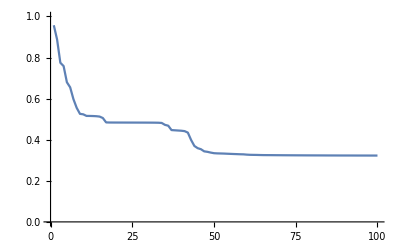

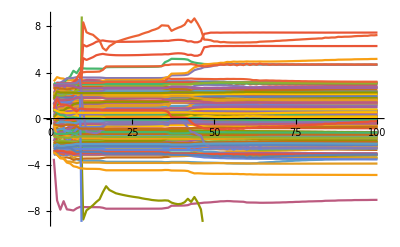

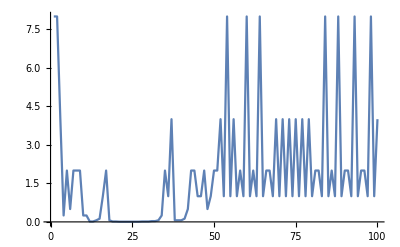

0.677113

```mathematica
DestroyAllQuregs[];

numQb =8;
hamil = getHamil[numQb];
aCirc = getCircuit @ trotterize[hamil,2,1,numQb];

(* DEBUG *)
(* bCirc = MapThread[Compose,{aCirc /. {R[ϕ_,σ_] :> (R[#,σ]&)},Table[Subscript[θ, t],{t,Length[aCirc]}]}]; *)
bCirc = getRecompCircuit[numQb]; 

numParams = bCirc⟦-1,1,2⟧;
initParams = Table[Subscript[θ, t]->RandomReal@{-π,π}, {t,numParams}];

{aψ, bψ, tψ} = CreateQuregs[numQb, 3];
dψ = CreateQuregs[numQb, numParams];

(* DEBUG *)
(* bCirc = RandomSample @ bCirc; *)
(* aCirc = Reverse @ bCirc /. Subscript[θ, _]:> 1; *)
(* initParams = Table[Subscript[θ, t]->-1.01, {t, numParams}]; *)

ApplyCircuit[aCirc, InitZeroState[aψ]]; 
SetQuregMatrix[tψ, getTrueEvol[hamil, GetQuregMatrix @ InitZeroState @ tψ, numQb]];
CalcFidelity[aψ, tψ]

ApplyCircuit[aCirc, InitZeroState[aψ]];
{eLog, θLog, ΔtLog} = simImag[aψ, bCirc, bψ, dψ, initParams, 100];

ListLinePlot[eLog, PlotRange->{0,1}]
ListLinePlot @ Transpose @ θLog
ListLinePlot @ ΔtLog
1 - calcEnergy[bψ]
```

```mathematica
ΔtLog[[-1]]
```

4.

```mathematica
data = <|"trotterfids"->{},"recompfids"->{}|>;

Do[
	Echo[numQb, "numQb: "];
	DestroyAllQuregs[];
	bCirc = getRecompCircuit[numQb];
	numParams = bCirc⟦-1,1,2⟧;
	{aψ, bψ, tψ} = CreateQuregs[numQb, 3];
	dψ = CreateQuregs[numQb, numParams];

	{timing,bothfids} = Timing @ Table[
		hamil = getHamil[numQb];
		(* SetQuregMatrix[tψ,getTrueEvol[hamil,GetQuregMatrix@InitZeroState@tψ, numQb]]; *)

		aCirc = getCircuit @ trotterize[hamil,2,1,numQb];
		ApplyCircuit[aCirc, InitZeroState[aψ]];

		initParams = Table[Subscript[θ, t]->RandomReal@{-π,π}, {t,numParams}]; 
		simImag[aψ, bCirc, bψ, dψ, initParams, 100];
		
		(* Trotter fidelity, recomp fidelity *)
		{"TROTTER_FID_NOT_COMPUTED", 1 - calcEnergy[bψ]} // Echo,

		20
	];
	{trotfids,recompfids} = Transpose[bothfids];

	Echo[timing, "duration: "];
	AppendTo[data["trotterfids"], trotfids];
	AppendTo[data["recompfids"], recompfids];

	Export["recomp_fids_from_14.txt", data];

	Null,
	{numQb,14,30}
]
```

numQb:  14

{TROTTER_FID_NOT_COMPUTED,0.0308225}

{TROTTER_FID_NOT_COMPUTED,0.305066}

{TROTTER_FID_NOT_COMPUTED,0.264135}

{TROTTER_FID_NOT_COMPUTED,0.162306}

{TROTTER_FID_NOT_COMPUTED,0.148687}

{TROTTER_FID_NOT_COMPUTED,0.102886}

{TROTTER_FID_NOT_COMPUTED,0.112406}

{TROTTER_FID_NOT_COMPUTED,0.102304}

{TROTTER_FID_NOT_COMPUTED,0.117193}

{TROTTER_FID_NOT_COMPUTED,0.239677}

{TROTTER_FID_NOT_COMPUTED,0.04289}

{TROTTER_FID_NOT_COMPUTED,0.137835}

{TROTTER_FID_NOT_COMPUTED,0.0636033}

{TROTTER_FID_NOT_COMPUTED,0.228033}

{TROTTER_FID_NOT_COMPUTED,0.265037}

{TROTTER_FID_NOT_COMPUTED,0.130019}

{TROTTER_FID_NOT_COMPUTED,0.116578}

{TROTTER_FID_NOT_COMPUTED,0.223932}

{TROTTER_FID_NOT_COMPUTED,0.178119}

{TROTTER_FID_NOT_COMPUTED,0.19183}

duration:  4651.36

numQb:  15

{TROTTER_FID_NOT_COMPUTED,0.425186}

{TROTTER_FID_NOT_COMPUTED,0.472649}

{TROTTER_FID_NOT_COMPUTED,0.409882}

{TROTTER_FID_NOT_COMPUTED,0.441947}

{TROTTER_FID_NOT_COMPUTED,0.385215}

{TROTTER_FID_NOT_COMPUTED,1.50343×10^-6}

{TROTTER_FID_NOT_COMPUTED,0.486501}

{TROTTER_FID_NOT_COMPUTED,1.52979×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.84984×10^-6}

{TROTTER_FID_NOT_COMPUTED,4.29792×10^-6}

{TROTTER_FID_NOT_COMPUTED,0.436971}

{TROTTER_FID_NOT_COMPUTED,0.46429}

{TROTTER_FID_NOT_COMPUTED,0.359157}

{TROTTER_FID_NOT_COMPUTED,0.489336}

{TROTTER_FID_NOT_COMPUTED,2.25847×10^-6}

{TROTTER_FID_NOT_COMPUTED,0.418359}

{TROTTER_FID_NOT_COMPUTED,0.400276}

{TROTTER_FID_NOT_COMPUTED,0.448952}

{TROTTER_FID_NOT_COMPUTED,0.324258}

{TROTTER_FID_NOT_COMPUTED,0.470362}

duration:  4957.91

numQb:  16

{TROTTER_FID_NOT_COMPUTED,0.952884}

{TROTTER_FID_NOT_COMPUTED,2.73269×10^-7}

{TROTTER_FID_NOT_COMPUTED,3.1822×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.74231×10^-6}

{TROTTER_FID_NOT_COMPUTED,0.951114}

{TROTTER_FID_NOT_COMPUTED,0.947524}

{TROTTER_FID_NOT_COMPUTED,0.940441}

{TROTTER_FID_NOT_COMPUTED,6.19275×10^-9}

{TROTTER_FID_NOT_COMPUTED,2.89473×10^-7}

{TROTTER_FID_NOT_COMPUTED,4.17844×10^-8}

{TROTTER_FID_NOT_COMPUTED,2.04476×10^-6}

{TROTTER_FID_NOT_COMPUTED,2.17206×10^-7}

{TROTTER_FID_NOT_COMPUTED,0.949057}

{TROTTER_FID_NOT_COMPUTED,0.947355}

{TROTTER_FID_NOT_COMPUTED,8.77256×10^-7}

{TROTTER_FID_NOT_COMPUTED,6.41924×10^-7}

{TROTTER_FID_NOT_COMPUTED,0.94207}

{TROTTER_FID_NOT_COMPUTED,8.04293×10^-7}

{TROTTER_FID_NOT_COMPUTED,8.73489×10^-9}

{TROTTER_FID_NOT_COMPUTED,1.5868×10^-6}

duration:  5331.47

numQb:  17

{TROTTER_FID_NOT_COMPUTED,0.0234916}

{TROTTER_FID_NOT_COMPUTED,0.00649185}

{TROTTER_FID_NOT_COMPUTED,0.00710768}

{TROTTER_FID_NOT_COMPUTED,0.00988526}

{TROTTER_FID_NOT_COMPUTED,4.20518×10^-7}

{TROTTER_FID_NOT_COMPUTED,0.0378961}

{TROTTER_FID_NOT_COMPUTED,0.0174856}

{TROTTER_FID_NOT_COMPUTED,0.00865964}

{TROTTER_FID_NOT_COMPUTED,0.018606}

{TROTTER_FID_NOT_COMPUTED,1.82436×10^-6}

{TROTTER_FID_NOT_COMPUTED,0.00855974}

{TROTTER_FID_NOT_COMPUTED,0.00950908}

{TROTTER_FID_NOT_COMPUTED,2.54205×10^-7}

{TROTTER_FID_NOT_COMPUTED,0.011818}

{TROTTER_FID_NOT_COMPUTED,0.0302384}

{TROTTER_FID_NOT_COMPUTED,0.0298894}

{TROTTER_FID_NOT_COMPUTED,1.15008×10^-6}

{TROTTER_FID_NOT_COMPUTED,0.0100083}

{TROTTER_FID_NOT_COMPUTED,0.000156214}

{TROTTER_FID_NOT_COMPUTED,0.0159503}

duration:  5771.21

numQb:  18

{TROTTER_FID_NOT_COMPUTED,4.76521×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.89449×10^-6}

{TROTTER_FID_NOT_COMPUTED,2.15652×10^-6}

{TROTTER_FID_NOT_COMPUTED,4.834×10^-7}

{TROTTER_FID_NOT_COMPUTED,0.157505}

{TROTTER_FID_NOT_COMPUTED,2.30132×10^-6}

{TROTTER_FID_NOT_COMPUTED,2.48319×10^-6}

{TROTTER_FID_NOT_COMPUTED,6.27937×10^-7}

{TROTTER_FID_NOT_COMPUTED,5.83442×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.45514×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.54779×10^-6}

{TROTTER_FID_NOT_COMPUTED,2.83363×10^-6}

{TROTTER_FID_NOT_COMPUTED,5.04953×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.02228×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.0544×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.73962×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.11794×10^-6}

{TROTTER_FID_NOT_COMPUTED,0.160771}

{TROTTER_FID_NOT_COMPUTED,4.94552×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.29883×10^-6}

duration:  6214.13

numQb:  19

{TROTTER_FID_NOT_COMPUTED,4.08179×10^-8}

{TROTTER_FID_NOT_COMPUTED,8.24917×10^-10}

{TROTTER_FID_NOT_COMPUTED,1.52135×10^-6}

{TROTTER_FID_NOT_COMPUTED,0.994101}

{TROTTER_FID_NOT_COMPUTED,6.2653×10^-8}

{TROTTER_FID_NOT_COMPUTED,2.46266×10^-9}

{TROTTER_FID_NOT_COMPUTED,1.02315×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.07246×10^-9}

{TROTTER_FID_NOT_COMPUTED,0.990247}

{TROTTER_FID_NOT_COMPUTED,1.88921×10^-7}

{TROTTER_FID_NOT_COMPUTED,0.995818}

{TROTTER_FID_NOT_COMPUTED,0.0519453}

{TROTTER_FID_NOT_COMPUTED,2.4423×10^-9}

{TROTTER_FID_NOT_COMPUTED,0.994054}

{TROTTER_FID_NOT_COMPUTED,2.62579×10^-8}

{TROTTER_FID_NOT_COMPUTED,2.28101×10^-8}

{TROTTER_FID_NOT_COMPUTED,1.29086×10^-8}

{TROTTER_FID_NOT_COMPUTED,6.59054×10^-8}

{TROTTER_FID_NOT_COMPUTED,7.34975×10^-8}

{TROTTER_FID_NOT_COMPUTED,3.39899×10^-7}

duration:  6643.84

numQb:  20

{TROTTER_FID_NOT_COMPUTED,1.02784×10^-7}

{TROTTER_FID_NOT_COMPUTED,1.15376×10^-6}

{TROTTER_FID_NOT_COMPUTED,2.0391×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.2772×10^-6}

{TROTTER_FID_NOT_COMPUTED,2.65532×10^-7}

{TROTTER_FID_NOT_COMPUTED,4.51754×10^-7}

{TROTTER_FID_NOT_COMPUTED,1.24874×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.48423×10^-7}

{TROTTER_FID_NOT_COMPUTED,7.93162×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.23509×10^-7}

{TROTTER_FID_NOT_COMPUTED,3.65808×10^-6}

{TROTTER_FID_NOT_COMPUTED,4.41205×10^-7}

{TROTTER_FID_NOT_COMPUTED,8.54541×10^-8}

{TROTTER_FID_NOT_COMPUTED,5.43655×10^-8}

{TROTTER_FID_NOT_COMPUTED,1.62921×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.07466×10^-7}

{TROTTER_FID_NOT_COMPUTED,8.95507×10^-7}

{TROTTER_FID_NOT_COMPUTED,1.28744×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.2822×10^-7}

{TROTTER_FID_NOT_COMPUTED,1.33367×10^-6}

duration:  7190.54

numQb:  21

{TROTTER_FID_NOT_COMPUTED,4.38771×10^-7}

{TROTTER_FID_NOT_COMPUTED,4.78498×10^-7}

{TROTTER_FID_NOT_COMPUTED,1.03366×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.96981×10^-7}

{TROTTER_FID_NOT_COMPUTED,8.72813×10^-9}

{TROTTER_FID_NOT_COMPUTED,4.97591×10^-8}

{TROTTER_FID_NOT_COMPUTED,1.763×10^-9}

{TROTTER_FID_NOT_COMPUTED,5.80597×10^-7}

{TROTTER_FID_NOT_COMPUTED,3.123×10^-7}

{TROTTER_FID_NOT_COMPUTED,1.88495×10^-7}

{TROTTER_FID_NOT_COMPUTED,1.92974×10^-8}

{TROTTER_FID_NOT_COMPUTED,4.8204×10^-7}

{TROTTER_FID_NOT_COMPUTED,1.21643×10^-6}

{TROTTER_FID_NOT_COMPUTED,1.60754×10^-8}

{TROTTER_FID_NOT_COMPUTED,8.63357×10^-8}

{TROTTER_FID_NOT_COMPUTED,4.80415×10^-8}

{TROTTER_FID_NOT_COMPUTED,5.35633×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.52297×10^-7}

{TROTTER_FID_NOT_COMPUTED,1.04073×10^-7}

{TROTTER_FID_NOT_COMPUTED,2.13199×10^-7}

duration:  7701.61

numQb:  22

LinkObject::linkd: Unable to communicate with closed link LinkObject['/home/tyson/Desktop/RecompilerScaling/Mathematica/quest_link_GPU',111,7].

LinkObject::linkn: Argument LinkObject['/home/tyson/Desktop/RecompilerScaling/Mathematica/quest_link_GPU',111,7] in LinkWrite[LinkObject['/home/tyson/Desktop/RecompilerScaling/Mathematica/quest_link_GPU',111,7],CallPacket[5,{0}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject['/home/tyson/Desktop/RecompilerScaling/Mathematica/quest_link_GPU',111,7] in LinkWrite[LinkObject['/home/tyson/Desktop/RecompilerScaling/Mathematica/quest_link_GPU',111,7],CallPacket[8,{1,0}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject['/home/tyson/Desktop/RecompilerScaling/Mathematica/quest_link_GPU',111,7] in LinkWrite[LinkObject['/home/tyson/Desktop/RecompilerScaling/Mathematica/quest_link_GPU',111,7],CallPacket[11,{1,0,-1}]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of LinkObject::linkn will be suppressed during this calculation.

Table::iterb: Iterator {dψdp,$Failed} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

«17 more identical outputs»

duration:  577.751

numQb:  23

Set::shape: Lists {aψ,bψ,tψ} and $Failed are not the same shape.

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

«17 more identical outputs»

duration:  633.07

numQb:  24

Set::shape: Lists {aψ,bψ,tψ} and $Failed are not the same shape.

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

«17 more identical outputs»

duration:  691.805

numQb:  25

Set::shape: Lists {aψ,bψ,tψ} and $Failed are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

«17 more identical outputs»

duration:  755.758

numQb:  26

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

«17 more identical outputs»

duration:  823.98

numQb:  27

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

«17 more identical outputs»

duration:  894.673

numQb:  28

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

«17 more identical outputs»

duration:  972.769

numQb:  29

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

«17 more identical outputs»

duration:  1050.7

numQb:  30

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

{TROTTER_FID_NOT_COMPUTED,Abs[$Failed]^2}

«17 more identical outputs»

duration:  1128.11

DEBUG

```mathematica
numQb = 14;
	Echo[numQb, "numQb: "];
	DestroyAllQuregs[];
	bCirc = getRecompCircuit[numQb];
	numParams = bCirc⟦-1,1,2⟧;
	{aψ, bψ, tψ} = CreateQuregs[numQb, 3];
	dψ = CreateQuregs[numQb, numParams];
```

numQb:  14

```mathematica
hamil = getHamil[numQb];
zerostate = GetQuregMatrix@InitZeroState@tψ;
```

```mathematica
getTrueEvol[hamil,zerostate, numQb]
```

```mathematica
SetQuregMatrix[tψ,getTrueEvol[hamil,GetQuregMatrix@InitZeroState@tψ, numQb]];
```

```mathematica
{timing,bothfids} = Timing @ Table[
		
		

		aCirc = getCircuit @ trotterize[hamil,2,1,numQb];
		ApplyCircuit[aCirc, InitZeroState[aψ]];
Time-adapative recompilation
		initParams = Table[Subscript[θ, t]->RandomReal@{-π,π}, {t,numParams}]; 
		simImag[aψ, bCirc, bψ, dψ, initParams, 100];
		
		(* Trotter fidelity, recomp fidelity *)
		{CalcFidelity[aψ,tψ], 1 - calcEnergy[bψ]} // Echo,

		20
	];
	{trotfids,recompfids} = Transpose[bothfids];

	Echo[timing, "duration: "];
	AppendTo[data["trotterfids"], trotfids];
	AppendTo[data["recompfids"], recompfids];
```